```mathematica
(*Copyright (c) 2023 Seiseki Akibue. All rights reserved.*)
```

```mathematica
(*target state {Cos[θ/2],Sin[θ/2]}*)
θ=RandomInteger[{0,12566}]/1000;
(*desired approximation error*)
err={1/4,1/25,1/400,1/2500,1/40000,1/250000,1/4000000,1/25000000,1/400000000,1/2500000000,1/40000000000,1/250000000000,1/4000000000000,1/25000000000000};
(*Directory*)
dir="C:/Users/Public";
(*file name*)
filename="sample";

(*system setting*)
precision=18;
ErrorForm[r_]:=TextString[SetPrecision[r 10^(-Floor[Log[10,r]]),precision]]<>"e-"<>TextString[(-Floor[Log[10,r]])]

(*program for deterministic synthesis*)
fname=FileNameJoin[{dir,filename<>"_det.bat"}];
str=OpenWrite[fname]
WriteLine[str,"gridsynth 0 > "<>filename<>"_det.txt"]
For[i=1,i<=Length[err],i++,
WriteLine[str,"gridsynth "<>TextString[Mod[SetPrecision[θ,precision],4π]]<>" -e "<>ErrorForm[err[[i]]]<>" >> "<>filename<>"_det.txt"]
]
Close[str] 
(*program for probabilistic synthesis*)
fname=FileNameJoin[{dir,filename<>"_prob.bat"}];
str=OpenWrite[fname]
WriteLine[str,"gridsynth 0 > "<>filename<>"_prob.txt"]
For[i=1,i<=Length[err],i++,
WriteLine[str,"gridsynth "<>TextString[Mod[SetPrecision[θ,precision],4π]]<>" -e "<>ErrorForm[0.3 √err[[i]]]<>" >> "<>filename<>"_prob.txt"];
WriteLine[str,"gridsynth "<>TextString[Mod[SetPrecision[θ,precision]+4ArcSin[SetPrecision[0.7 √err[[i]],18]],4π]]<>" -e "<>ErrorForm[0.3 √err[[i]]]<>" >> "<>filename<>"_prob.txt"];
WriteLine[str,"gridsynth "<>TextString[Mod[SetPrecision[θ,precision]-4ArcSin[SetPrecision[0.7 √err[[i]],18]],4π]]<>" -e "<>ErrorForm[0.3 √err[[i]]]<>" >> "<>filename<>"_prob.txt"];
]
Close[str] 
θ=ToExpression[TextString[Mod[SetPrecision[θ,precision],4π]]]
```

OutputStream[…]

C:\Users\Public\sample_det.bat

OutputStream[…]

C:\Users\Public\sample_prob.bat

7.116

```mathematica
(*Actual and desired approximation errors and T-count achieved by a deterministic synthesis*)
id=({{1, 0}, {0, 1}});
f[gate_]:=If[gate=="T",({{1, 0}, {0, Exp[I π/4]}}),If[gate=="S",({{1, 0}, {0, I}}),If[gate=="H",1/(√2)({{1, 1}, {1, -1}}),If[gate=="X",({{0, 1}, {1, 0}}),id]]]]
pureDop[v_]:=v.ConjugateTranspose[v]
precision=100;
targetstate=pureDop[{{Cos[θ/2]},{Sin[θ/2]}}];
Seqlist=StringSplit[Import[dir<>"/"<>filename<>"_det.txt"],"\n"];
DETacterr=Table[
Seq=Characters[Seqlist[[j]]];
U=SetPrecision[id,precision];
For[i=Length[Seq],i>=1,i--,U=f[Seq[[i]]].U];
synthstate=pureDop[N[f["S"].f["H"].U.f["H"].{{1},{0}}]];
{Max[Eigenvalues[targetstate-synthstate]],Count[Seq,"T"]}
,{j,2,Length[Seqlist]}]
DETdeserr=Table[{N[err[[i]]],DETacterr[[i]][[2]]},{i,1,Length[Seqlist]-1}]
```

{{0.209227,4},{0.0253024,10},{0.0018754,26},{0.000262616,34},{0.0000149444,48},{1.57457×10^-6,50},{2.10858×10^-7,68},{2.29801×10^-8,74},{1.36227×10^-9,86},{2.85752×10^-10,96},{1.18288×10^-11,106},{6.56018×10^-13,112},{2.35759×10^-13,128},{3.10044×10^-14,132}}

{{0.25,4},{0.04,10},{0.0025,26},{0.0004,34},{0.000025,48},{4.×10^-6,50},{2.5×10^-7,68},{4.×10^-8,74},{2.5×10^-9,86},{4.×10^-10,96},{2.5×10^-11,106},{4.×10^-12,112},{2.5×10^-13,128},{4.×10^-14,132}}

```mathematica
(*Actual and desired approximation errors and T-count achieved by a probabilistic synthesis*)
id=({{1, 0}, {0, 1}});
f[gate_]:=If[gate=="T",({{1, 0}, {0, Exp[I π/4]}}),If[gate=="S",({{1, 0}, {0, I}}),If[gate=="H",1/(√2)({{1, 1}, {1, -1}}),If[gate=="X",({{0, 1}, {1, 0}}),id]]]]
pureDop[v_]:=v.ConjugateTranspose[v]
precision=100;
targetstate=pureDop[{{Cos[θ/2]},{Sin[θ/2]}}];
Seqlistp=StringSplit[Import[dir<>"/"<>filename<>"_prob.txt"],"\n"];
PROBacterr=Table[
Seqp=Table[Characters[Seqlistp[[3j+k+1]]],{k,1,3}];
Tcount=Max[Table[Count[Seqp[[k]],"T"],{k,1,3}]];
synthstate=Table[U=SetPrecision[id,precision];
For[i=Length[Seqp[[k]]],i>=1,i--,U=f[Seqp[[k]][[i]]].U];
pureDop[N[f["S"].f["H"].U.f["H"].{{1},{0}}]]
,{k,1,3}];
tri=Triangle[Table[1/2{Tr[Re[synthstate[[k]]].({{0, 1}, {1, 0}})],Tr[Re[synthstate[[k]]].({{1, 0}, {0, -1}})]},{k,1,3}]];
{RegionDistance[tri,1/2{Tr[targetstate.({{0, 1}, {1, 0}})],Tr[targetstate.({{1, 0}, {0, -1}})]}],Tcount}
,{j,0,Length[err]-1}]
PROBdeserr=Table[{N[err[[j]]],PROBacterr[[j]][[2]]},{j,1,Length[err]}]
```

{{0.0513512,8},{0.00438661,10},{0.000359902,18},{0.0000602271,22},{3.8139×10^-6,30},{6.36639×10^-7,34},{4.21893×10^-8,42},{1.92681×10^-8,46},{1.17029×10^-10,50},{4.25621×10^-11,60},{2.13566×10^-12,58},{5.01088×10^-13,62},{7.60105×10^-14,68},{1.09773×10^-14,74}}

{{0.25,8},{0.04,10},{0.0025,18},{0.0004,22},{0.000025,30},{4.×10^-6,34},{2.5×10^-7,42},{4.×10^-8,46},{2.5×10^-9,50},{4.×10^-10,60},{2.5×10^-11,58},{4.×10^-12,62},{2.5×10^-13,68},{4.×10^-14,74}}

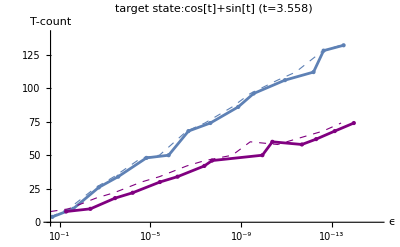

```mathematica
Show[
ListLinePlot[DETacterr,PlotLabel->"target state:cos[t]+sin[t] (t="<>TextString[θ/2]<>")",AxesLabel->{"ϵ","T-count"},Mesh->All,MeshStyle->Directive[PointSize[Medium]],ScalingFunctions->{"ReverseLog",None},PlotRange->{{0.25,10^(-15)},{0,140}},Ticks->{Table[{10^k,Superscript[10,k]},{k,-1,-15,-2}],Automatic}],
ListLinePlot[DETdeserr,PlotStyle->{Thickness[0.002],Dashed},ScalingFunctions->{"ReverseLog",None}],
ListLinePlot[PROBacterr,PlotStyle->{Purple},Mesh->All,MeshStyle->Directive[PointSize[Medium]],ScalingFunctions->{"ReverseLog",None}],ListLinePlot[PROBdeserr,PlotStyle->{Thickness[0.002],Dashed,Purple},ScalingFunctions->{"ReverseLog",None}]
]
```